```mathematica
Quit[]
```

```mathematica
$Assumptions=α∈Reals&&α>0&&m∈Reals&&m>0&&λ∈Reals;
```

```mathematica
ω[p_]:=(*√(m^2+p^2)*)p^2/(2m);Nx=5;max=100;
```

```mathematica
m =5/2;λ=π/2;
```

```mathematica
Clear@α
```

```mathematica
α=(*0.33375*)0.5;
```

```mathematica
ϕ[n_][p_]:=√(α/(√π 2^n n!)) HermiteH[n,α p] E^(1/2 (-α^2) p^2)
```

```mathematica
H[n_][p_?NumberQ]:=ω[p]ϕ[n][p]-λ/1 NIntegrate[(ϕ[n][k]-ϕ[n][p]-(k-p)ϕ[n]'[p])/(p-k)^2,{k,-max,0,max}]
```

```mathematica
Table[NIntegrate[ϕ[2i][p]H[2n][p],{p,-max,max},MaxRecursion->50],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
Sort@Eigenvalues[Last[%]]
```

{302.249,{{1.77637,-0.440889,-0.284163,-0.15564,-0.103991,-0.0767313},{-0.396451,5.46448,-0.0753178,-0.330181,-0.161772,-0.100763},{-0.284152,0.033561,8.28254,0.357436,-0.386376,-0.18124},{-0.155639,-0.330141,0.529634,10.8396,0.840991,-0.437595},{-0.103991,-0.161772,-0.38629,1.07632,13.2552,1.35844},{-0.0767313,-0.100763,-0.18124,-0.437445,1.65686,15.5785}}}

{1.71213,5.49174,8.15931,10.4708,13.0333,16.3294}

```mathematica
NIntegrate[ϕ[5][p]H[2][p],{p,-max,max},MaxRecursion->10]
```

```mathematica
NIntegrate[ϕ[10][p]H[10][p],{p,-max,max},MaxRecursion->50]//Timing
```

{8.40625,30.7992}

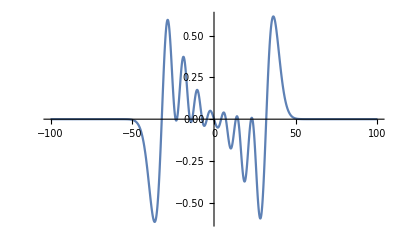

```mathematica
Plot[ϕ[6][p]H[9][p],{p,-100,100},PlotRange->All]
```

```mathematica
Last@%19//MatrixForm
```

(6.72374 | 0 | 3.4277 | 0 | -0.975301 | 0 | 0.41917 | 0 | -0.293982 | 0 | 0.169398 | 0 | -0.145569 | 0 | 0.0912165 | 0 | -0.0872037 | 0 | 0.0562689 | 0 | -0.0579406 | 0 | 0.03761 | 0 | -0.0411226 | 0
0 | 12.1597 | 0 | 4.21381 | 0 | -1.00159 | 0 | 0.395163 | 0 | -0.249204 | 0 | 0.140854 | 0 | -0.110203 | 0 | 0.0702679 | 0 | -0.0609734 | 0 | 0.0411676 | 0 | -0.0381055 | 0 | 0.026529 | 0 | -0.0257252
3.47236 | 0 | 15.2069 | 0 | 5.14578 | 0 | -1.24789 | 0 | 0.498974 | 0 | -0.324987 | 0 | 0.18399 | 0 | -0.14977 | 0 | 0.0942759 | 0 | -0.0858464 | 0 | 0.0563766 | 0 | -0.0553223 | 0 | 0.0368978 | 0
0 | 4.29142 | 0 | 18.0185 | 0 | 5.80019 | 0 | -1.34677 | 0 | 0.525327 | 0 | -0.32777 | 0 | 0.184837 | 0 | -0.143551 | 0 | 0.0916168 | 0 | -0.0789891 | 0 | 0.0534725 | 0 | -0.0491879 | 0 | 0.0343748
-0.975036 | 0 | 5.25591 | 0 | 20.2878 | 0 | 6.4667 | 0 | -1.51308 | 0 | 0.592683 | 0 | -0.375839 | 0 | 0.211705 | 0 | -0.168252 | 0 | 0.106331 | 0 | -0.094508 | 0 | 0.0627265 | 0 | -0.0599836 | 0
0 | -1.00099 | 0 | 5.94287 | 0 | 22.4249 | 0 | 7.01772 | 0 | -1.61385 | 0 | 0.625853 | 0 | -0.388079 | 0 | 0.218676 | 0 | -0.169003 | 0 | 0.107996 | 0 | -0.0926799 | 0 | 0.0628965 | 0 | -0.0575825
0.419174 | 0 | -1.24684 | 0 | 6.64207 | 0 | 24.3081 | 0 | 7.56276 | 0 | -1.7462 | 0 | 0.678066 | 0 | -0.424473 | 0 | 0.238754 | 0 | -0.187297 | 0 | 0.118768 | 0 | -0.104076 | 0 | 0.0695879 | 0
0 | 0.395176 | 0 | -1.34514 | 0 | 7.22597 | 0 | 26.1025 | 0 | 8.04441 | 0 | -1.84188 | 0 | 0.711828 | 0 | -0.439685 | 0 | 0.247738 | 0 | -0.190813 | 0 | 0.122098 | 0 | -0.104421 | 0 | 0.0710274
-0.293982 | 0 | 0.499 | 0 | -1.51076 | 0 | 7.8041 | 0 | 27.7456 | 0 | 8.51628 | 0 | -1.95502 | 0 | 0.755694 | 0 | -0.469668 | 0 | 0.264144 | 0 | -0.205576 | 0 | 0.130738 | 0 | -0.11352 | 0
0 | -0.249204 | 0 | 0.525372 | 0 | -1.61068 | 0 | 8.31907 | 0 | 29.3235 | 0 | 8.94806 | 0 | -2.04497 | 0 | 0.788491 | 0 | -0.485807 | 0 | 0.273801 | 0 | -0.210372 | 0 | 0.134797 | 0 | -0.114977
0.169398 | 0 | -0.324986 | 0 | 0.592755 | 0 | -1.74206 | 0 | 8.82451 | 0 | 30.7992 | 0 | 9.36963 | 0 | -2.14554 | 0 | 0.827013 | 0 | -0.511739 | 0 | 0.287924 | 0 | -0.222916 | 0 | 0.142121 | 0
0 | 0.140854 | 0 | -0.327768 | 0 | 0.625963 | 0 | -1.83662 | 0 | 9.29011 | 0 | 32.2242 | 0 | 9.76351 | 0 | -2.23026 | 0 | 0.858434 | 0 | -0.528008 | 0 | 0.297719 | 0 | -0.228333 | 0 | 0.146499
-0.145569 | 0 | 0.183991 | 0 | -0.375835 | 0 | 0.678226 | 0 | -1.94848 | 0 | 9.74577 | 0 | 33.5749 | 0 | 10.1477 | 0 | -2.32186 | 0 | 0.893195 | 0 | -0.551141 | 0 | 0.310286 | 0 | -0.239361 | 0
0 | -0.110203 | 0 | 0.184837 | 0 | -0.388074 | 0 | 0.712051 | 0 | -2.037 | 0 | 10.174 | 0 | 34.8845 | 0 | 10.5116 | 0 | -2.40203 | 0 | 0.923183 | 0 | -0.567201 | 0 | 0.319983 | 0 | -0.245072
0.0912165 | 0 | -0.14977 | 0 | 0.211705 | 0 | -0.424464 | 0 | 0.755997 | 0 | -2.13597 | 0 | 10.5929 | 0 | 36.1371 | 0 | 10.8665 | 0 | -2.48685 | 0 | 0.955118 | 0 | -0.588275 | 0 | 0.331421 | 0
0 | 0.0702679 | 0 | -0.143551 | 0 | 0.218677 | 0 | -0.439671 | 0 | 0.788891 | 0 | -2.21893 | 0 | 10.9917 | 0 | 37.3557 | 0 | 11.2059 | 0 | -2.56308 | 0 | 0.983733 | 0 | -0.603983 | 0 | 0.340912
-0.0872037 | 0 | 0.0942759 | 0 | -0.168252 | 0 | 0.238755 | 0 | -0.469649 | 0 | 0.827533 | 0 | -2.30858 | 0 | 11.3819 | 0 | 38.5288 | 0 | 11.5371 | 0 | -2.64258 | 0 | 1.01344 | 0 | -0.623473 | 0
0 | -0.0609734 | 0 | 0.0916168 | 0 | -0.169003 | 0 | 0.247739 | 0 | -0.485779 | 0 | 0.859098 | 0 | -2.38661 | 0 | 11.7568 | 0 | 39.6731 | 0 | 11.856 | 0 | -2.71542 | 0 | 1.04077 | 0 | -0.638772
0.0562689 | 0 | -0.0858464 | 0 | 0.106331 | 0 | -0.187297 | 0 | 0.264145 | 0 | -0.5117 | 0 | 0.89403 | 0 | -2.4691 | 0 | 12.1239 | 0 | 40.7801 | 0 | 12.1674 | 0 | -2.79063 | 0 | 1.06865 | 0
0 | 0.0411676 | 0 | -0.0789891 | 0 | 0.107996 | 0 | -0.190813 | 0 | 0.273804 | 0 | -0.527954 | 0 | 0.924222 | 0 | -2.54279 | 0 | 12.479 | 0 | 41.8623 | 0 | 12.4687 | 0 | -2.86053 | 0 | 1.0948
-0.0579406 | 0 | 0.0563766 | 0 | -0.094508 | 0 | 0.118768 | 0 | -0.205576 | 0 | 0.287927 | 0 | -0.551069 | 0 | 0.956396 | 0 | -2.61953 | 0 | 12.827 | 0 | 42.9131 | 0 | 12.7633 | 0 | -2.9322 | 0
0 | -0.0381055 | 0 | 0.0534725 | 0 | -0.0926799 | 0 | 0.122098 | 0 | -0.210371 | 0 | 0.297724 | 0 | -0.567106 | 0 | 0.985288 | 0 | -2.68938 | 0 | 13.1652 | 0 | 43.9423 | 0 | 13.0494 | 0 | -2.99956
0.03761 | 0 | -0.0553223 | 0 | 0.0627265 | 0 | -0.104076 | 0 | 0.130738 | 0 | -0.222915 | 0 | 0.310294 | 0 | -0.588151 | 0 | 1.01532 | 0 | -2.76136 | 0 | 13.4971 | 0 | 44.9448 | 0 | 13.3293 | 0
0 | 0.026529 | 0 | -0.0491879 | 0 | 0.0628965 | 0 | -0.104421 | 0 | 0.134797 | 0 | -0.228333 | 0 | 0.319994 | 0 | -0.603822 | 0 | 1.04302 | 0 | -2.82778 | 0 | 13.8208 | 0 | 45.9281 | 0 | 13.6021
-0.0411226 | 0 | 0.0368978 | 0 | -0.0599836 | 0 | 0.0695879 | 0 | -0.11352 | 0 | 0.142121 | 0 | -0.23936 | 0 | 0.331436 | 0 | -0.623267 | 0 | 1.07134 | 0 | -2.8957 | 0 | 14.1389 | 0 | 46.8882 | 0
0 | -0.0257252 | 0 | 0.0343748 | 0 | -0.0575825 | 0 | 0.0710274 | 0 | -0.114977 | 0 | 0.146499 | 0 | -0.24507 | 0 | 0.340933 | 0 | -0.63851 | 0 | 1.09797 | 0 | -2.95904 | 0 | 14.4501 | 0 | 47.8313)

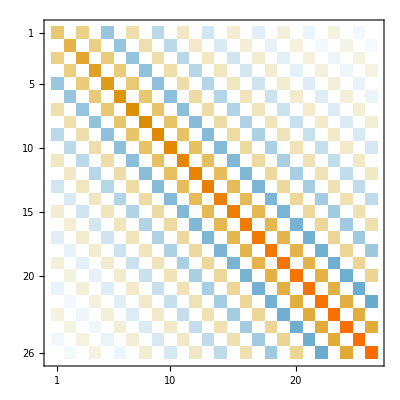

```mathematica
MatrixPlot[%21]
```